## Stationary points and their positions

```mathematica
Quit[]
```

### Hamiltonian 3 sites

```mathematica
hamiltonian[j_,u_,p1_,q1_,p2_,q2_]:=-j((q1+q2)√(2  - q1^2-q2^2-p1^2-p2^2) + q1 q2 + p1 p2 ) + u/4((2  - q1^2-q2^2-p1^2-p2^2)^2 + (q1^2+p1^2)^2+(q2^2+p2^2)^2)
```

```mathematica
variables={p1,q1,p2,q2}
error=10^-4;
chopTolerance=10^-5;
numGuess=5000;
path="d:\\results\\bh\\";
```

{p1,q1,p2,q2}

```mathematica
Clear[u,j];
u=1;
minj=-1;
maxj=1;
stepj=0.005;
```

### Hamiltonian 4 sites

```mathematica
hamiltonian[j_,u_,p1_,q1_,p2_,q2_,p3_,q3_]:=-j((q1+q3)√(2  - q1^2-q2^2-q3^2-p1^2-p2^2-p3^2) + q1 q2 + p1 p2 +  q2 q3 + p2 p3 ) + u/4((2  - q1^2-q2^2-q3^2-p1^2-p2^2-p3^2)^2 + (q1^2+p1^2)^2+(q2^2+p2^2)^2+(q3^2+p3^2)^2)
```

```mathematica
variables={p1,q1,p2,q2,p3,q3}
error=10^-4;
chopTolerance=10^-5;
numGuess=20000;
path="d:\\results\\bh\\";
```

{p1,q1,p2,q2,p3,q3}

```mathematica
Clear[u,j];
u=1;
minj=-1;
maxj=1;
stepj=0.005;
```

### Hamiltonian 5 sites

```mathematica
hamiltonian[j_,u_,p1_,q1_,p2_,q2_,p3_,q3_,p4_,q4_]:=-j((q1+q4)√(2  - q1^2-q2^2-q3^2-q4^2-p1^2-p2^2-p3^2-p4^2) + q1 q2 + p1 p2 +  q2 q3 + p2 p3 +q3 q4+p3 p4) + u/4((2  - q1^2-q2^2-q3^2-q4^2-p1^2-p2^2-p3^2-p4^2)^2 + (q1^2+p1^2)^2+(q2^2+p2^2)^2+(q3^2+p3^2)^2+(q4^2+p4^2)^2)
```

```mathematica
variables={p1,q1,p2,q2,p3,q3,p4,q4}
error=10^-4;
chopTolerance=10^-5;
numGuess=200000;
path="d:\\results\\bh\\";
```

```mathematica
Clear[u,j];
u=1;
minj=-1;
maxj=1;
stepj=0.005;
```

{p1,q1,p2,q2,p3,q3,p4,q4}

### Hamiltonian 6 sites

```mathematica
hamiltonian[j_,u_,p1_,q1_,p2_,q2_,p3_,q3_,p4_,q4_,p5_,q5_]:=-j((q1+q5)√(2  - q1^2-q2^2-q3^2-q4^2-q5^2-p1^2-p2^2-p3^2-p4^2-p5^2) + q1 q2 + p1 p2 +  q2 q3 + p2 p3 +q3 q4+p3 p4+q4 q5+p4 p5) + u/4((2  - q1^2-q2^2-q3^2-q4^2-q5^2-p1^2-p2^2-p3^2-p4^2-p5^2)^2 + (q1^2+p1^2)^2+(q2^2+p2^2)^2+(q3^2+p3^2)^2+(q4^2+p4^2)^2+(q5^2+p5^2)^2)
```

```mathematica
variables={p1,q1,p2,q2,p3,q3,p4,q4,p5,q5}
error=10^-4;
chopTolerance=10^-5;
numGuess=1000000;
path="d:\\results\\bh\\";
```

{p1,q1,p2,q2,p3,q3,p4,q4,p5,q5}

```mathematica
Clear[u,j];
u=1;
minj=-1;
maxj=1;
stepj=0.005;
```

### Hamiltonian 7 sites

```mathematica
hamiltonian[j_,u_,p1_,q1_,p2_,q2_,p3_,q3_,p4_,q4_,p5_,q5_,p6_,q6_]:=-j((q1+q5)√(2  - q1^2-q2^2-q3^2-q4^2-q5^2-q6^2-p1^2-p2^2-p3^2-p4^2-p5^2-p6^2) + q1 q2 + p1 p2 +  q2 q3 + p2 p3 +q3 q4+p3 p4+q4 q5+p4 p5+q5 q6+p5 p6) + u/4((2  - q1^2-q2^2-q3^2-q4^2-q5^2-q6^2-p1^2-p2^2-p3^2-p4^2-p5^2-p6^2)^2 + (q1^2+p1^2)^2+(q2^2+p2^2)^2+(q3^2+p3^2)^2+(q4^2+p4^2)^2+(q5^2+p5^2)^2+(q6^2+p6^2)^2)
```

```mathematica
variables={p1,q1,p2,q2,p3,q3,p4,q4,p5,q5,p6,q6}
error=10^-4;
chopTolerance=10^-5;
numGuess=1000000;
path="d:\\results\\bh\\";
```

{p1,q1,p2,q2,p3,q3,p4,q4,p5,q5,p6,q6}

```mathematica
Clear[u,j];
u=1;
minj=-1;
maxj=1;
stepj=0.005;
```

### Hamiltonian 10 sites

```mathematica
hamiltonian[j_,u_,p1_,q1_,p2_,q2_,p3_,q3_,p4_,q4_,p5_,q5_,p6_,q6_,p7_,q7_,p8_,q8_,p9_,q9_]:=-j((q1+q9)√(2  - q1^2-q2^2-q3^2-q4^2-q5^2-q6^2-q7^2-q8^2-q9^2-p1^2-p2^2-p3^2-p4^2-p5^2-p6^2-p7^2-p8^2-p9^2) + q1 q2 + p1 p2 +  q2 q3 + p2 p3 +q3 q4+p3 p4+q4 q5+p4 p5+q5 q6+p5 p6+q6 q7+p6 p7+q7 q8+p7 p8+q8 q9+p8 p9) + u/4((2  - q1^2-q2^2-q3^2-q4^2-q5^2-q6^2-q7^2-q8^2-q9^2-p1^2-p2^2-p3^2-p4^2-p5^2-p6^2-p7^2-p8^2-p9^2)^2 + (q1^2+p1^2)^2+(q2^2+p2^2)^2+(q3^2+p3^2)^2+(q4^2+p4^2)^2+(q5^2+p5^2)^2+(q6^2+p6^2)^2+(q7^2+p7^2)^2+(q8^2+p8^2)^2+(q9^2+p9^2)^2)
```

```mathematica
variables={p1,q1,p2,q2,p3,q3,p4,q4,p5,q5,p6,q6,p7,q7,p8,q8,p9,q9}
error=10^-3;
numGuess=1000000;
path="d:\\results\\bh\\";
```

{p1,q1,p2,q2,p3,q3,p4,q4,p5,q5,p6,q6,p7,q7,p8,q8,p9,q9}

```mathematica
Clear[u,j];
u=1;
minj=-1;
maxj=1;
stepj=0.005;
```

### General numerical calculation

#### Equations

```mathematica
(* Arguments of the hamiltonian *)
arguments =Join[{j,u},variables];
derivatives=FullSimplify/@D[hamiltonian@@arguments,#]&/@variables
hessian=FullSimplify/@D[derivatives,#]&/@variables;
(* Right sides of the Hamilton equations of motion *) 
hamilton=derivatives*Table[(-1)^(i+1),{i,Length[derivatives]}];
(* Stability matrix of the Hamiltonian dynamics *)
stability=FullSimplify/@D[hamilton,#]&/@Flatten[Reverse/@Partition[variables,2]];
(* Equations to solve *)
equations=(#==0)&/@derivatives;
(* Particle numbers in each dimension *)
ns=(#1^2+#2^2)&@@@Partition[variables,2]
normalisation=Total[#^2&/@variables];
dim=Length[variables]
```

{-j p2+(j p1 (q1+q2))/(√(2-p1^2-p2^2-q1^2-q2^2))+p1 (-2+2 p1^2+p2^2+2 q1^2+q2^2),q1 (-2+2 p1^2+p2^2+2 q1^2+q2^2)-j (q2-(q1 (q1+q2))/(√(2-p1^2-p2^2-q1^2-q2^2))+√(2-p1^2-p2^2-q1^2-q2^2)),-j p1+(j p2 (q1+q2))/(√(2-p1^2-p2^2-q1^2-q2^2))+p2 (-2+p1^2+2 p2^2+q1^2+2 q2^2),q2 (-2+p1^2+2 p2^2+q1^2+2 q2^2)-j (q1-(q2 (q1+q2))/(√(2-p1^2-p2^2-q1^2-q2^2))+√(2-p1^2-p2^2-q1^2-q2^2))}

{p1^2+q1^2,p2^2+q2^2}

4

#### Parallel calculation

```mathematica
LaunchKernels[16];
```

```mathematica
result=ParallelTable[Module[{guess,solutions,t,sol},
solutions={};
t=Timing[Do[
(* Initial guess for FindRoot *)
guess=RandomReal[{-√2,√2},dim];
If[guess.guess<2,Quiet[sol=Chop[FindRoot[equations,Transpose[{variables, guess}]],chopTolerance]];
(* Basic checks of the solution reality and validity *)
If[Abs[normalisation/.sol]<2&&Total[Abs[derivatives]/.sol]<error&&Total[Abs[Im[derivatives]]/.sol]==0,
solutions=Append[solutions,sol]]],
{i,1,numGuess} ];
(* Basic removal of identical solutions *)
solutions=Union[solutions,SameTest->(Norm[Values[#1]-Values[#2]]<error&)]][[1]];
If[Length[solutions]>0,
{
(* Info about the calculation *)
{j,t,Length[solutions]},
(* Stationary point energies *)
Tuples[{{j},hamiltonian@@arguments/.solutions}],
(* Stationary point positions *)
Tuples[{{j},#/. solutions}]&/@variables,
(* Number of excitations at stationary points *)
Tuples[{{j},#/. solutions}]&/@ns,
(* Twice the number of negative signs from 0 to dim + 1; odd numbers mean zero eigenvalues *)
Tuples[{{j},(-Total[Sign[Chop[Eigenvalues[#],chopTolerance]]]+dim)&/@(hessian/.solutions)}],
(* Number of real eigenvalues of the stability matrix *)
Tuples[{{j},Count[Chop[Eigenvalues[#],chopTolerance],x_/;Im[x]==0]&/@(stability/.solutions)}]
}]],{j,minj,maxj,stepj},Method->"FinestGrained"];
```

#### Reordering

```mathematica
(* First let's precalculate dimensions *)
nstable=Table[0,2dim+1];
nsaddle=Table[0,2dim+1];
nunstable=Table[0,2dim+1];
l=Length[result];
```

```mathematica
Monitor[Do[Do[
i=result[[r,5,f,2]];
s=result[[r,6,f,2]];
If[IntegerQ[i],
If[s==0,nstable[[i+1]]++,
If[s==dim,nunstable[[i+1]]++,nsaddle[[i+1]]++]
]],{f,1,result[[r,1,3]]}
],{r,1,l}],r]
```

```mathematica
nstable
nsaddle
nunstable
```

{636,0,0,0,904,0,0,0,903}

{0,0,698,0,0,418,691,0,0}

{0,0,1088,0,87,0,0,0,0}

```mathematica
(* Then allocate tables *)
hstable=Table[{},2dim+1];Do[hstable[[k]]=Table[{},nstable[[k]]],{k,1,2dim+1}]
hsaddle=Table[{},2dim+1];Do[hsaddle[[k]]=Table[{},nsaddle[[k]]],{k,1,2dim+1}]
hunstable=Table[{},2dim+1];Do[hunstable[[k]]=Table[{},nunstable[[k]]],{k,1,2dim+1}]
tstable=Table[{},2dim+1];Do[tstable[[k]]=Table[{},dim/2 nstable[[k]]],{k,1,2dim+1}]
tsaddle=Table[{},2dim+1];Do[tsaddle[[k]]=Table[{},dim/2 nsaddle[[k]]],{k,1,2dim+1}]
tunstable=Table[{},2dim+1];
Do[tunstable[[k]]=Table[{},dim/2 nunstable[[k]]],{k,1,2dim+1}]
xstable=Table[{},2dim+1];Do[xstable[[k]]=Table[{},nstable[[k]]],{k,1,2dim+1}]
xsaddle=Table[{},2dim+1];Do[xsaddle[[k]]=Table[{},nsaddle[[k]]],{k,1,2dim+1}]
xunstable=Table[{},2dim+1];Do[xunstable[[k]]=Table[{},nunstable[[k]]],{k,1,2dim+1}]
```

```mathematica
istable=Table[1,2dim+1];
isaddle=Table[1,2dim+1];
iunstable=Table[1,2dim+1];
```

```mathematica
(* Tak v tomto kódu se vyzná jen prase *)
```

```mathematica
Monitor[Do[Do[
i=result[[r,5,f,2]];
s=result[[r,6,f,2]];
If[IntegerQ[i],
x=Table[result[[r,3,k,f,2]],{k,1,dim}];
PrependTo[x,result[[r,1,1]]];
If[s==0,
hstable[[i+1,istable[[i+1]]]]=result[[r,2,f]];
xstable[[i+1,istable[[i+1]]]]=x;
Do[tstable[[i+1,dim/2(istable[[i+1]]-1)+k]]=result[[r,4,k,f]],{k,1,dim/2}];istable[[i+1]]++,
If[s==dim,
hunstable[[i+1,iunstable[[i+1]]]]=result[[r,2,f]];
xunstable[[i+1,iunstable[[i+1]]]]=x;
Do[tunstable[[i+1,dim/2(iunstable[[i+1]]-1)+k]]=result[[r,4,k,f]],{k,1,dim/2}];iunstable[[i+1]]++,
hsaddle[[i+1,isaddle[[i+1]]]]=result[[r,2,f]];
xsaddle[[i+1,isaddle[[i+1]]]]=x;
Do[tsaddle[[i+1,dim/2(isaddle[[i+1]]-1)+k]]=result[[r,4,k,f]],{k,1,dim/2}];isaddle[[i+1]]++
]]],{f,1,result[[r,1,3]]}
],{r,1,l}],r]
```

#### Remove duplicates

```mathematica
hstable=Sort[#]&/@hstable;
hunstable=Sort[#]&/@hunstable;
hsaddle=Sort[#]&/@hsaddle;
```

```mathematica
hstable=DeleteAdjacentDuplicates[#,Norm[#1-#2]<error&]&/@hstable;
hunstable=DeleteAdjacentDuplicates[#,Norm[#1-#2]<error&]&/@hunstable;
hsaddle=DeleteAdjacentDuplicates[#,Norm[#1-#2]<error&]&/@hsaddle;
```

```mathematica
Length[#]&/@hstable
Length[#]&/@hsaddle
Length[#]&/@hunstable
```

{400,0,0,0,429,0,0,0,413}

{0,0,230,0,0,1,301,0,0}

{0,0,1,0,87,0,0,0,0}

```mathematica
tstable=Sort[#]&/@tstable;
tunstable=Sort[#]&/@tunstable;
tsaddle=Sort[#]&/@tsaddle;
```

```mathematica
tstable=DeleteAdjacentDuplicates[#,Norm[#1-#2]<error&]&/@tstable;
tunstable=DeleteAdjacentDuplicates[#,Norm[#1-#2]<error&]&/@tunstable;
tsaddle=DeleteAdjacentDuplicates[#,Norm[#1-#2]<error&]&/@tsaddle;
```

```mathematica
Length[#]&/@tstable
Length[#]&/@tsaddle
Length[#]&/@tunstable
```

{400,0,0,0,658,0,0,0,668}

{0,0,459,0,0,2,604,0,0}

{0,0,1,0,87,0,0,0,0}

#### Plots

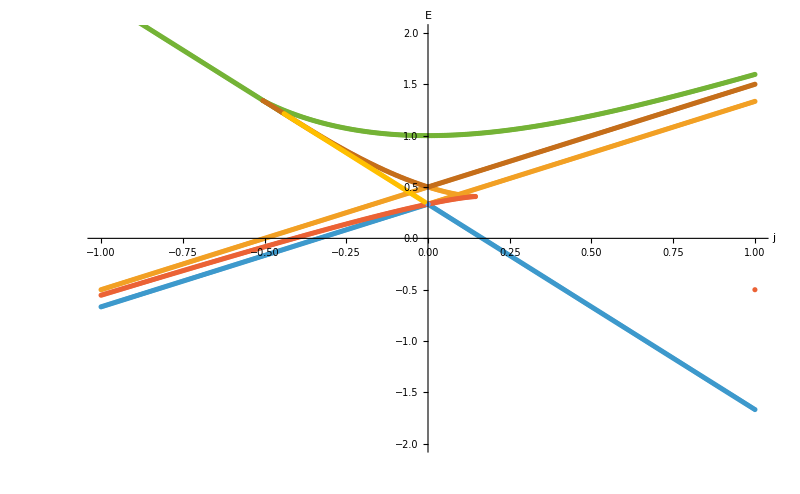

```mathematica
hp=ListPlot[Join[Select[hstable,Length[#]>0&],Select[hsaddle,Length[#]>0&],Select[hunstable,Length[#]>0&]],PlotRange->{-2,2},AxesLabel->{"j","E"},ImageSize->800]
```

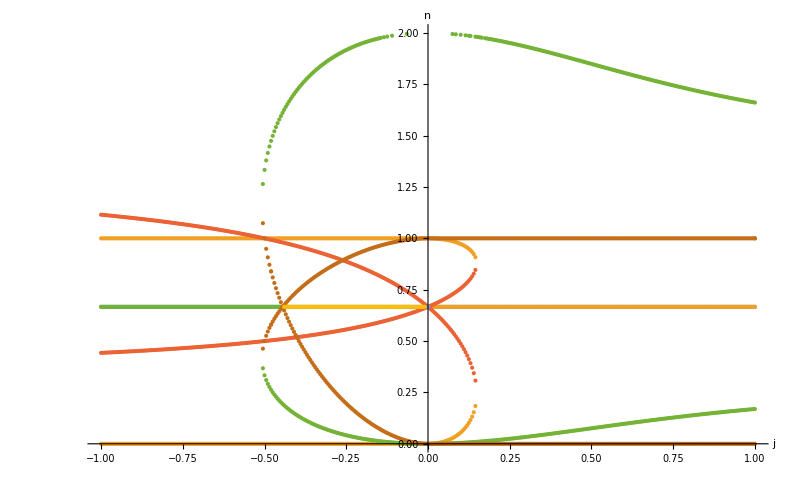

```mathematica
tp=ListPlot[Join[Select[tstable,Length[#]>0&],Select[tsaddle,Length[#]>0&],Select[tunstable,Length[#]>0&]],PlotRange->{0,2},AxesLabel->{"j","n"},ImageSize->800]
```

#### Saving

```mathematica
Do[Export[path<>ToString[dim/2+1]<>"\\hstable_" <>ToString[f-1] <> ".txt",N[hstable[[f]]],"CSV"],{f,1,2dim+1}];
Do[Export[path<>ToString[dim/2+1]<>"\\hunstable_" <>ToString[f-1] <> ".txt",N[hunstable[[f]]],"CSV"],{f,1,2dim+1}];
Do[Export[path<>ToString[dim/2+1]<>"\\hsaddle_" <>ToString[f-1] <> ".txt",N[hsaddle[[f]]],"CSV"],{f,1,2dim+1}];
```

```mathematica
Do[Export[path<>ToString[dim/2+1]<>"\\tstable_" <>ToString[f-1] <> ".txt",N[tstable[[f]]],"CSV"],{f,1,2dim+1}];
Do[Export[path<>ToString[dim/2+1]<>"\\tunstable_" <>ToString[f-1] <> ".txt",N[tunstable[[f]]],"CSV"],{f,1,2dim+1}];
Do[Export[path<>ToString[dim/2+1]<>"\\tsaddle_" <>ToString[f-1] <> ".txt",N[tsaddle[[f]]],"CSV"],{f,1,2dim+1}];
```

```mathematica
Do[Export[path<>ToString[dim/2+1]<>"\\xstable_" <>ToString[f-1] <> ".txt",N[xstable[[f]]],"CSV"],{f,1,2dim+1}];
Do[Export[path<>ToString[dim/2+1]<>"\\xunstable_" <>ToString[f-1] <> ".txt",N[xunstable[[f]]],"CSV"],{f,1,2dim+1}];
Do[Export[path<>ToString[dim/2+1]<>"\\xsaddle_" <>ToString[f-1] <> ".txt",N[xsaddle[[f]]],"CSV"],{f,1,2dim+1}];
```

```mathematica
Export[path<>ToString[dim/2+1]<>"\\h.pdf",hp];
Export[path<>ToString[dim/2+1]<>"\\t.pdf",tp];
```

```mathematica
Export[path<>ToString[dim/2+1]<>"\\h.png",hp];
Export[path<>ToString[dim/2+1]<>"\\t.png",tp];
```

### Testing

```mathematica
j=1
u=RandomReal[{-1,1}]
guess=RandomReal[{-√2,√2},dim]
```

1

0.485415

{0.127979,0.305455,1.1797,-0.421213,-1.29525,-0.050505,-0.627583,-1.15828,0.686276,-0.181624,1.04563,-0.39503,-0.941819,-1.3851,1.27209,-1.02386,0.487171,-0.104084}

```mathematica
sol=Chop[FindRoot[equations,Transpose[{variables, guess}]],error]
normalisation/.sol
Total[Abs[derivatives]/.sol]
Total[Abs[Im[derivatives]]/.sol]==0
Chop[Eigenvalues[hessian/.sol]]
-Total[Sign[Chop[Eigenvalues[hessian/.sol],error]]]/2+dim/2
Chop[Eigenvalues[stability/.sol]]
Count[Chop[Eigenvalues[stability/.sol],error],x_/;Im[x]==0]
```

{p1→0,q1→0.447214,p2→0,q2→0.447214,p3→0,q3→0.447214,p4→0,q4→0.447214,p5→0,q5→0.447214,p6→0,q6→0.447214,p7→0,q7→0.447214,p8→0,q8→0.447214,p9→0,q9→0.447214}

1.8

4.82947×10^-15

True

{24.9277,4.07218,3.90211,3.8122,3.61803,3.18769,3.17557,2.8122,2.61803,2.,1.84797,1.57613,1.38197,0.824429,0.682814,0.576132,0.381966,0.097887}

0

{0.+4.09593 ⅈ,0.-4.09593 ⅈ,0.+3.71385 ⅈ,0.-3.71385 ⅈ,0.+3.71385 ⅈ,0.-3.71385 ⅈ,0.+2.71338 ⅈ,0.-2.71338 ⅈ,0.+2.71338 ⅈ,0.-2.71338 ⅈ,0.+1.47586 ⅈ,0.-1.47586 ⅈ,0.+1.47586 ⅈ,0.-1.47586 ⅈ,0.+0.469109 ⅈ,0.-0.469109 ⅈ,0.+0.469109 ⅈ,0.-0.469109 ⅈ}

0

```mathematica
solutions={}
```

{}

```mathematica
u=-0.5;
j=1;
```

```mathematica
Do[guess=RandomReal[{-√2,√2},dim];
If[guess.guess<2,Quiet[sol=Chop[FindRoot[equations,Transpose[{variables, guess}]]]];
If[Abs[normalisation/.sol]<2&& Total[Abs[derivatives]/.sol]<error&&Total[Abs[Im[derivatives]]/.sol]==0,
solutions=Append[solutions,sol]]],{i,1,numGuess} ];
solutions=Union[solutions,SameTest->(Norm[Values[#1]-Values[#2]]<error&)]
```

{{p1→-0.5,q1→0.288675,p2→-0.5,q2→-0.288675,p3→0,q3→-0.57735,p4→0.5,q4→-0.288675,p5→0.5,q5→0.288675},{p1→-0.5,q1→-0.288675,p2→0.5,q2→-0.288675,p3→0,q3→0.57735,p4→-0.5,q4→-0.288675,p5→0.5,q5→-0.288675},{p1→0,q1→-0.57735,p2→0,q2→0.57735,p3→0,q3→-0.57735,p4→0,q4→0.57735,p5→0,q5→-0.57735},{p1→0,q1→-0.428801,p2→0,q2→-0.428801,p3→0,q3→0.795147,p4→0,q4→-0.428801,p5→0,q5→-0.428801},{p1→0,q1→-0.383348,p2→0,q2→-0.840291,p3→0,q3→-0.383348,p4→0,q4→0.383348,p5→0,q5→0.840291},{p1→0,q1→0,p2→0,q2→-0.707107,p3→0,q3→0.707107,p4→0,q4→0,p5→0,q5→-0.707107},{p1→0,q1→0.428801,p2→0,q2→-0.795147,p3→0,q3→0.428801,p4→0,q4→0.428801,p5→0,q5→-0.795147},{p1→0,q1→0.57735,p2→0,q2→0.57735,p3→0,q3→0.57735,p4→0,q4→0.57735,p5→0,q5→0.57735},{p1→0,q1→0.840291,p2→0,q2→0.383348,p3→0,q3→-0.383348,p4→0,q4→-0.840291,p5→0,q5→-0.383348},{p1→0.5,q1→-0.288675,p2→-0.5,q2→-0.288675,p3→0,q3→0.57735,p4→0.5,q4→-0.288675,p5→-0.5,q5→-0.288675}}